# Fourier transform

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

## Fourier transform

```mathematica
f[t_]=ⅇ^(-2 t^2);
```

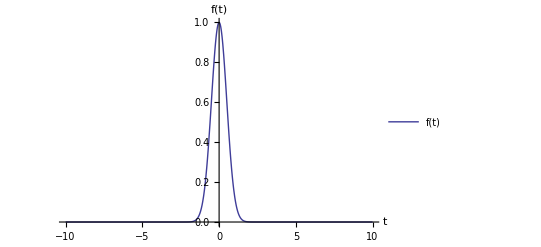

```mathematica
Plot[f[t],{t,-10,10}, PlotRange -> All,PlotLegends->"Expressions",AxesLabel->{"t","f(t)"}]
```

```mathematica
F[ω_]=FourierTransform[f[t], t,ω]
```

1/2 ⅇ^(-ω^2/8)

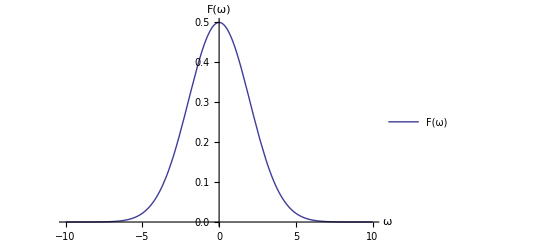

```mathematica
Plot[F[ω],{ω,-10,10}, PlotRange -> All,PlotLegends->"Expressions",AxesLabel->{"ω","F(ω)"}]
```

## Inverse Fourier transform

```mathematica
InverseFourierTransform[F[ω],ω,t]
```

ⅇ^(-2 t^2)